```mathematica
1+1
```

2

```mathematica
EE[a_]=√(om 1/a^3+(1-om) F[a])
```

√(om/a^3+(1-om) F[a])

```mathematica
Ωm[a_]=om/(EE[a]^2 a^3)
```

om/(a^3 (om/a^3+(1-om) F[a]))

```mathematica
(* Fix Omega and gamma_0 *)
```

```mathematica
om=0.3;γ0=0.555;
```

```mathematica
(* Compute q0 versus gamma prime *)
```

```mathematica
Do[{γ1[i]=-0.05+i*0.005;γ[a_]=γ0+γ1[i] (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,2/3,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];q0[i]=q[0]},{i,0,20}]
```

```mathematica
(* Make table with pairs (γ',q0) *)
```

```mathematica
set=Table[{γ1[i],q0[i]},{i,0,20}]
```

{{-0.05,-0.178179},{-0.045,-0.232905},{-0.04,-0.287631},{-0.035,-0.342358},{-0.03,-0.397084},{-0.025,-0.45181},{-0.02,-0.506536},{-0.015,-0.561262},{-0.01,-0.615988},{-0.005,-0.670714},{0.,-0.72544},{0.005,-0.780166},{0.01,-0.834892},{0.015,-0.889618},{0.02,-0.944344},{0.025,-0.99907},{0.03,-1.0538},{0.035,-1.10852},{0.04,-1.16325},{0.045,-1.21797},{0.05,-1.2727}}

```mathematica
Y=Interpolation[%]
```

InterpolatingFunction[…]

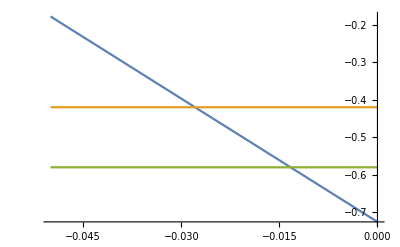

```mathematica
Plot[{Y[z],-0.5+0.08,-0.5-0.08},{z,-0.05,0}]
```

```mathematica
(* Compute the allowed range for gamma prime *)
```

```mathematica
FindRoot[Y[z]==-0.5+0.08,{z,-0.028}]
```

{z→-0.0279063}

```mathematica
FindRoot[Y[z]==-0.5-0.08,{z,-0.013}]
```

{z→-0.013288}

```mathematica
(* View solution for one extreme *)
```

```mathematica
γ1=-0.013288;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];w[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

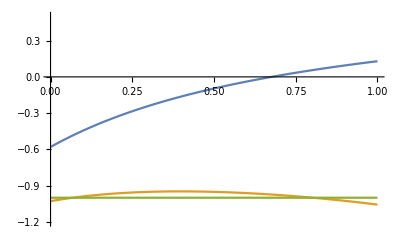

```mathematica
Plot[{q[z],w[z],-1},{z,0.001,1.0},PlotRange->{-1.2,0.5}]
```

```mathematica
(* Analytic expression: Fitting with polynomials *)
```

```mathematica
setF=Table[{z,Fz[z]},{z,0.001,1,0.001}];
```

```mathematica
P1=Fit[setF,{1,z},z]
```

0.99596+0.069009 z

```mathematica
w1[z_]=-1+(1+z) D[P1,z]/(3 P1)//Simplify
```

(-14.099-0.666667 z)/(14.4323+1. z)

```mathematica
P2=Fit[setF,{1,z,z^2},z]
```

0.984979+0.134767 z-0.0656926 z^2

```mathematica
w2[z_]=-1+(1+z) D[P2,z]/(3 P2)//Simplify
```

(14.3099+2.03432 z-0.333333 z^2)/(-14.9937-2.05148 z+1. z^2)

```mathematica
P3=Fit[setF,{1,z,z^2,z^3},z]
```

0.996318-0.000829291 z+0.272791 z^2-0.22543 z^3

```mathematica
w3[z_]=-1+(1+z) D[P3,z]/(3 P3)//Simplify
```

(4.42085-0.809179 z+1.40336 z^2-1.11022×10^-16 z^3)/(-4.41962+0.0036787 z-1.21009 z^2+1. z^3)

```mathematica
P4=Fit[setF,{1,z,z^2,z^3,z^4},z]
```

0.999164-0.057434 z+0.526961 z^2-0.620279 z^3+0.197227 z^4

```mathematica
w4[z_]=-1+(1+z) D[P4,z]/(3 P4)//Simplify
```

(-5.16312+1.97537 z-4.03561 z^2+1.33333 z^3+0.333333 z^4)/(5.06605-0.291207 z+2.67185 z^2-3.145 z^3+1. z^4)

```mathematica
P5=Fit[setF,{1,z,z^2,z^3,z^4,z^5},z]
```

0.999792-0.076147 z+0.65756 z^2-0.967934 z^3+0.58785 z^4-0.156093 z^5

```mathematica
w5[z_]=-1+(1+z) D[P5,z]/(3 P5)//Simplify
```

(6.56771-3.13363 z+7.60521 z^2-5.02136 z^3+0.411325 z^4+0.666667 z^5)/(-6.4051+0.487831 z-4.21262 z^2+6.20101 z^3-3.76602 z^4+1. z^5)

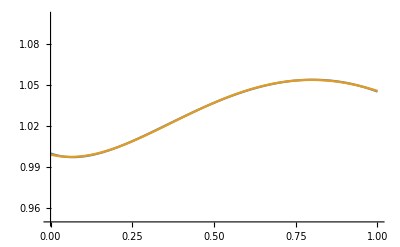

```mathematica
Plot[{Fz[z],P4},{z,0.001,1},PlotRange->{0.95,1.1}]
```

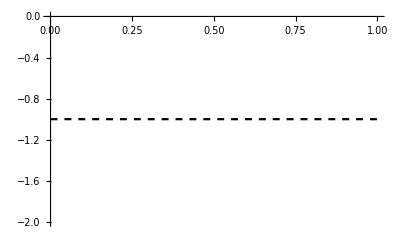

```mathematica
line=Plot[-1,{z,0.001,1},PlotStyle->{Dashed,Black}]
```

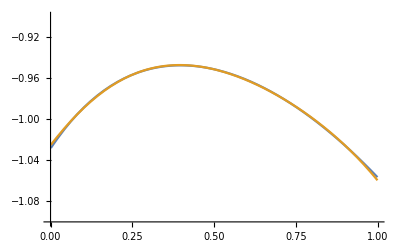

```mathematica
pl3=Plot[{w[z],w5[z]},{z,0.001,0.999},PlotRange->{-1.1,-0.9}]
```

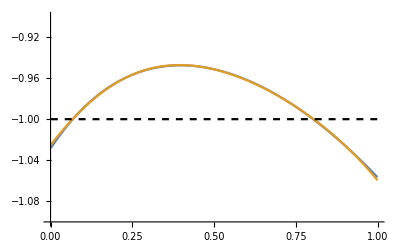

```mathematica
Show[pl3,line]
```

```mathematica
(* View solution for the other extreme *)
```

```mathematica
γ1=-0.027906;
```

```mathematica
γ[a_]=γ0+γ1 (-1+1/a);f[a_]=Ωm[a]^γ[a];eq=a f'[a]+f[a]^2+f[a] (2+a EE'[a]/EE[a] )-(3 Ωm[a])/2;sol=NDSolve[{eq==0,F[1]==1},F,{a,1/2,1}];Fa[a_]=F[a]/.Flatten[sol];Fz[z_]:=Fa[1/(1+z)];w[z_]:=-1+((1+z) Fz'[z])/(3 Fz[z]);hz[z_]:=√(om (1+z)^3+(1-om) Fz[z]);
q[z_]:=-1+((1+z) hz'[z])/hz[z];
```

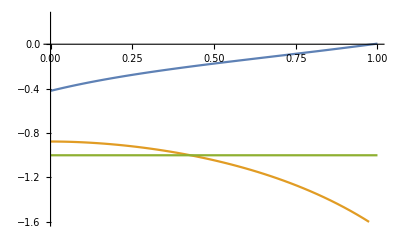

```mathematica
Plot[{q[z],w[z],-1},{z,0.001,1.0},PlotRange->{-1.6,0.25}]
```

```mathematica
(* Fitting *)
```

```mathematica
setF=Table[{z,Fz[z]},{z,0,1,0.001}];
```

```mathematica
P1=Fit[setF,{1,z},z]
```

1.09842-0.125198 z

```mathematica
w1[z_]=-1+(1+z) D[P1,z]/(3 P1)//Simplify
```

(9.10682-0.666667 z)/(-8.77349+1. z)

```mathematica
P2=Fit[setF,{1,z,z^2},z]
```

0.988254+0.536479 z-0.661678 z^2

```mathematica
w2[z_]=-1+(1+z) D[P2,z]/(3 P2)//Simplify
```

(1.2233+1.20719 z-0.333333 z^2)/(-1.49356-0.810787 z+1. z^2)

```mathematica
P3=Fit[setF,{1,z,z^2,z^3},z]
```

0.997149+0.429474 z-0.39403 z^2-0.178431 z^3

```mathematica
w3[z_]=-1+(1+z) D[P3,z]/(3 P3)//Simplify
```

(4.7861+3.07683 z+0.263899 z^2-2.22045×10^-16 z^3)/(-5.58842-2.40694 z+2.2083 z^2+1. z^3)

```mathematica
P4=Fit[setF,{1,z,z^2,z^3,z^4},z]
```

0.999995+0.372284 z-0.136373 z^2-0.579365 z^3+0.200467 z^4

```mathematica
w4[z_]=-1+(1+z) D[P4,z]/(3 P4)//Simplify
```

(-4.36931-1.69158 z-2.66332 z^2+1.33333 z^3+0.333333 z^4)/(4.98834+1.85709 z-0.680279 z^2-2.89008 z^3+1. z^4)

```mathematica
P5=Fit[setF,{1,z,z^2,z^3,z^4,z^5},z]
```

0.999954+0.373521 z-0.145051 z^2-0.556208 z^3+0.174409 z^4+0.0104231 z^5

```mathematica
w5[z_]=-1+(1+z) D[P5,z]/(3 P5)//Simplify
```

(-83.9909-33.168 z-48.7242 z^2+22.3105 z^3+7.2443 z^4+0.666667 z^5)/(95.9362+35.8358 z-13.9162 z^2-53.3629 z^3+16.7329 z^4+1. z^5)

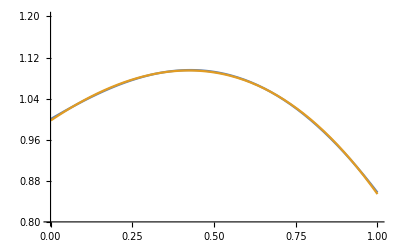

```mathematica
Plot[{Fz[z],P3},{z,0.001,1},PlotRange->{0.8,1.2}]
```

```mathematica
line=Plot[-1,{z,0.001,1},PlotStyle->{Dashed,Black}]
```

-Graphics-

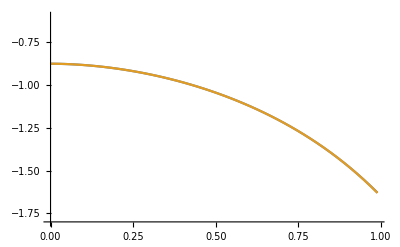

```mathematica
pl3=Plot[{w[z],w4[z]},{z,0.001,0.99},PlotRange->{-1.8,-0.6}]
```

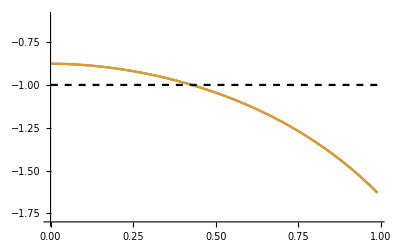

```mathematica
Show[pl3,line]
```